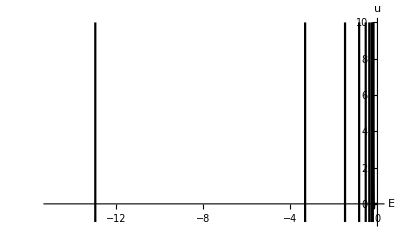

FindRoot::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

General::stop: 在本次计算中，FindRoot::brmp 的进一步输出将被抑制.

{12.2085,Null}

E->{{e→-12.9465},{e→-3.34907},{e→-1.48763},{e→-0.840345},{e→-0.539192}}

```mathematica
V[r_]:=-143996/(10000r)+ Subscript[V, s][r]
Subscript[V, s][r_]:=0.1/r^2
u0=10^-6;α=262713/1000000;
f[e_?NumberQ(*/;e∈Reals*)]:=
Block[{u,r,r1=200,r2=10^-6},
First[u[r2]/.
NDSolve[{u''[r]+(α(e-V[r])-0/r^2)u[r]==0,u[r1]==u0,(*u'[r1]==√(α(V[r1]-e)) u0*)u'[r1]==-10^-6},
u,{r,r1,r2}(*,MaxSteps->10^6,WorkingPrecision->20,MaxStepFraction->10^-3*),Method->"Chasing"]]]
Plot[{f[e]},{e,-15,0},
(*PlotRange->{{-15,0},{-10,10}(*,{-10^-3,10^-3}*)},*)
AxesLabel->{"E","u"},
PlotStyle->Black,PlotPoints->100,PlotRange->{{-15,0},{-1,10}}]
ew={
(*NSolve[f[e]==0,e,Reals];*)
FindRoot[f[e]==0,{e,-15,-14}(*,MaxIterations->10000,WorkingPrecision->20*)],
(*FindRoot[f[e]==0,{e,-5,-3},MaxIterations->1000,WorkingPrecision->20],*)
(*FindRoot[f[e]==0,{e,-14,-13}(*,MaxIterations->10000,WorkingPrecision->20*)],
FindRoot[f[e]==0,{e,-13,-12}(*,MaxIterations->10000,WorkingPrecision->20*)],*)
FindRoot[f[e]==0,{e,-7,-6}(*,MaxIterations->10000,WorkingPrecision->20*)],
(*FindRoot[f[e]==0,{e,-3,-2},MaxIterations->10000,WorkingPrecision->20],*)
FindRoot[f[e]==0,{e,-2,-1}(*,MaxIterations->10000,WorkingPrecision->20*)],
FindRoot[f[e]==0,{e,-1,-0.75}],
FindRoot[f[e]==0,{e,-0.6,-0.5}]
};//AbsoluteTiming
(*ew={
FindRoot[f[e]==0,{e,-3,-2}],
FindRoot[f[e]==0,{e,-2,-1}],
FindRoot[f[e]==0,{e,-1,-0.75}]
}*)
(*f[e]/.{First[ew]//Flatten}*)
Print["E->",ew]
(*f[1]*)
(*Clear["Global`*"]*)
```

```mathematica
Table[-13.6/n^2+0.2/((2l+1)a^2 n^3),{n,5}]/.{l->0,a->0.529}
```

{-12.8853,-3.31066,-1.48464,-0.838833,-0.538282}

```mathematica
s=Table[e/.ew[[i]],{i,5}]
Table[(s[[i]]-%55[[i]])/s[[i]] 100"%",{i,5}]
Correlation[s,%55]
AbsoluteCorrelation[s,%55]
```

{-12.9465,-3.34907,-1.48763,-0.840345,-0.539192}

{0.472517 %,1.1469 %,0.200812 %,0.1799 %,0.168726 %}

0.999998

```mathematica
Correlation
```

36.2222

```mathematica
Table[2/((2l+1)a^2 n^3),{n,5}]/.{l->0,a->0.529}
```

{7.14692,0.893364,0.264701,0.111671,0.0571753}

```mathematica
Table[e/.{{{e->-9.61325224526779},{e->-9.209303815947402},{e->-2.7731112589989375},{e->-1.3166780151112327},{e->-0.7661486046626703}}[[n]]},{n,5}]
```

{{-9.61325},{-9.2093},{-2.77311},{-1.31668},{-0.766149}}

```mathematica
Flatten[{{-9.61325224526779},{-9.209303815947402},{-2.7731112589989375},{-1.3166780151112327},{-0.7661486046626703}}]
```

{-9.61325,-9.2093,-2.77311,-1.31668,-0.766149}